## AutoCAD Bulge Arcs

Given an arc defined by a start point A, end point B, and a bulge factor b, find the equivalent radius r, start angle θ, and end angle ϕ.

### Given Parameters

```mathematica
A={0,0}; B={x,y};
```

We use inverse trigonometric functions extensively in this notebook, so we’ll disable those warning messages:

```mathematica
SetOptions[Solve, InverseFunctions->True];
```

This is a function used to accumulate solution rules.

```mathematica
solutions={};
Solution[r_Rule] := (solutions = Join[solutions, {r}]; r);
Solution[{r_}] := Solution[r];
```

### Setup

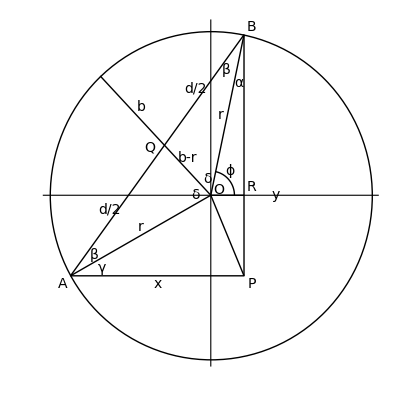

Let O be the origin of the circle encompassing the arc (calculated later).
Let P form a right triangle with respect to A and B:

```mathematica
P={B⟦1⟧,A⟦2⟧}
```

{x,0}

Let Q be the midpoint of OverBar[AB]:

```mathematica
Q={B⟦1⟧/2,B⟦2⟧/2}
```

{x/2,y/2}

### Solution

The length d of OverBar[AB] is found by solving the Pythagorean theorem for triangle APB:

```mathematica
d->√(x^2+y^2)//Solution
```

d→√(x^2+y^2)

The radius r of the circle is found by solving the Pythagorean theorem for triangle AOQ:

```mathematica
Solve[(d/2)^2+(r-b)^2==r^2,r]//Solution
```

r→(4 b^2+d^2)/(8 b)

Using the law of sines on AOQ, angle β can be found:

```mathematica
(r-b)/Sin[β]==r/Sin[π/2]⇒(r-b)/Sin[β]==r/1⇒Sin[β]==r/(r-b)
```

```mathematica
Solve[(r-b)/r==Sin[β],β]//Solution
```

β→ArcSin[(-b+r)/r]

Angle δ is the complement of β:

```mathematica
δ->π/2-β//Solution
```

δ→π/2-β

Angle ABP is β + α and can be found through the definition of the tangent function:

```mathematica
Solve[Tan[β+α]==x/y,α]⟦1,1⟧//Solution
```

α→-β+ArcTan[x/y]

Considering triangle ORB, we can see that the end angle ϕ is the complement of α:

```mathematica
ϕ->π/2-α//Solution;
ϕ //. solutions
```

π/2+ArcSin[(8 b (-b+(4 b^2+x^2+y^2)/(8 b)))/(4 b^2+x^2+y^2)]-ArcTan[x/y]

The start angle θ is angle ROA, or

```mathematica
θ->ϕ+2δ//Solution;
θ //. solutions
```

π/2+2 (π/2-ArcSin[(8 b (-b+(4 b^2+x^2+y^2)/(8 b)))/(4 b^2+x^2+y^2)])+ArcSin[(8 b (-b+(4 b^2+x^2+y^2)/(8 b)))/(4 b^2+x^2+y^2)]-ArcTan[x/y]

### Supplement

```mathematica
Solve[Tan[β+γ]==y/x,γ]//Solution
```

γ→-β+ArcTan[y/x]

We need to set Origin directly here; otherwise, Mathematica assumes it’s a scalar and doesn’t perform vector addition properly.

```mathematica
Origin={r Cos[γ],r Sin[γ]}
```

{r Cos[γ],r Sin[γ]}

Z is the extension of OverVector[OQ] to meet the circle perimeter.

```mathematica
Module[{result},result=Solve[{
r^2==(cx-ox)^2+(cy-oy)^2,
cy==-y/x(cx-x/2)+y/2}, {cx, cy}];(cx/.result⟦1⟧)-(cx/.result⟦2⟧)]
```

(ox x^2-oy x y+x y^2-√(-oy^2 x^4+r^2 x^4-2 ox oy x^3 y+2 oy x^4 y-ox^2 x^2 y^2+r^2 x^2 y^2+2 ox x^3 y^2-x^4 y^2))/(x^2+y^2)-(ox x^2-oy x y+x y^2+√(-oy^2 x^4+r^2 x^4-2 ox oy x^3 y+2 oy x^4 y-ox^2 x^2 y^2+r^2 x^2 y^2+2 ox x^3 y^2-x^4 y^2))/(x^2+y^2)

```mathematica
Z={cx,cy}/.Solve[{
r^2==(cx-Origin⟦1⟧)^2+(cy-Origin⟦2⟧)^2,
cy==-y/x(cx-x/2)+y/2}, {cx, cy}]⟦1⟧
```

{1/(2 (x^2+y^2))(2 x y^2+2 r x^2 Cos[γ]-2 r x y Sin[γ]-√((-2 x y^2-2 r x^2 Cos[γ]+2 r x y Sin[γ])^2-4 (x^2+y^2) (x^2 y^2-2 r x^2 y Sin[γ]))),(x y-(x y^3)/(x^2+y^2)-(r x^2 y Cos[γ])/(x^2+y^2)+(r x y^2 Sin[γ])/(x^2+y^2)+(y √((-2 x y^2-2 r x^2 Cos[γ]+2 r x y Sin[γ])^2-4 (x^2+y^2) (x^2 y^2-2 r x^2 y Sin[γ])))/(2 (x^2+y^2)))/x}

```mathematica
demo ={x->11, y->15, b->6}
```

{x→11,y→15,b→6}

```mathematica
AOAngle=ArcTan[Origin⟦1⟧-A⟦1⟧,Origin⟦2⟧-A⟦2⟧] //. Join[solutions,demo];
OQAngle=ArcTan[Q⟦1⟧-Origin⟦1⟧,Q⟦2⟧-Origin⟦2⟧] //. Join[solutions,demo];
ABAngle=ArcTan[B⟦1⟧-A⟦1⟧,B⟦2⟧-A⟦2⟧] //. Join[solutions,demo];
OBAngle=ArcTan[B⟦1⟧-Origin⟦1⟧,B⟦2⟧-Origin⟦2⟧] //. Join[solutions,demo];
```

```mathematica
r//.Join[solutions,demo]
```

-245/24

```mathematica
Show[
Graphics[{
Thickness[Large],
Circle[Origin, r],
Line[{A, B}],
Line[{A, Origin,B}],
Line[{A, {B⟦1⟧, A⟦2⟧}, B}],
Line[{Origin, Z}],
Line[{Origin, P}],
Line[{Origin,{B⟦1⟧,Origin⟦2⟧}}],
Text[Style["A", Italic,14], A-{.5,.5}],
Text[Style["B", Italic, 14], B + {.5, .5}],
Text[Style["O", Italic, 14], Origin + {.5, .3}],
Text[Style["P", Italic, 14], P+{.5,-.5}],
Text[Style["Q", Italic, 14], Q+{-.5,.5}],
Text[Style["R", Italic, 14], {B⟦1⟧+.5,Origin⟦2⟧+.5}],
Text[Style["β", 14], A + {1.5, 1.3}],
Text[Style["β", 14], B - {1.1, 2.2}],
Text[Style["α", 14], B - {0.3, 3}],
Text[Style["γ", 14], A + {2, .5}],
Text[Style["δ", 14], Origin+{-1,0}],
Text[Style["δ", 14], Origin+{-.2,1}],
Text[Style["ϕ", 14], Origin+{1.2,1.5}],
Rotate[Text[Style["b", Italic, 14], Q+{-1,3}],-OQAngle+π/2],
Rotate[Text[Style["r", Italic, 14], 0.5 (A+Origin) +{0,.5}], AOAngle],
Rotate[Text[Style["r", Italic, 14], 0.5 (B+Origin) +{-.4,0}], OBAngle],
Rotate[Text[Style["b-r", Italic, 14], Q+{1.9,-0.2}],-OQAngle+π/2+.1],
Rotate[Text[Style["d/2", Italic, 14], 0.5 (A+Q)+{-.3, 0.4}], ABAngle],
Rotate[Text[Style["d/2", Italic, 14], 0.5 (Q+B)+{-.3, 0.4}], ABAngle],
Text[Style["x",Italic,14], 0.5(A+P)-{0,.5}],
Text[Style["y",Italic,14], {B⟦1⟧+2,Origin⟦2⟧}],
Circle[Origin,1.5,{0,OBAngle}]
}//.Join[solutions,demo]], Axes->True, AxesOrigin->(Origin//. Join[solutions,demo]), Ticks->None]
```

-Graphics-

```mathematica
demo ={x->11, y->15, b->-6}
```

{x→11,y→15,b→-6}

```mathematica
AOAngle=ArcTan[Origin⟦1⟧-A⟦1⟧,Origin⟦2⟧-A⟦2⟧] //. Join[solutions,demo];
OQAngle=ArcTan[Q⟦1⟧-Origin⟦1⟧,Q⟦2⟧-Origin⟦2⟧] //. Join[solutions,demo];
ABAngle=ArcTan[B⟦1⟧-A⟦1⟧,B⟦2⟧-A⟦2⟧] //. Join[solutions,demo];
OBAngle=ArcTan[B⟦1⟧-Origin⟦1⟧,B⟦2⟧-Origin⟦2⟧] //. Join[solutions,demo];
```

```mathematica
N[Z]//.Join[solutions,demo]
```

{6.43279-9.4805 ⅈ,6.22802+12.928 ⅈ}

```mathematica
Show[
Graphics[{
Thickness[Large],
Circle[Origin,- Abs[r]],
Line[{A, B}],
Line[{A, Origin,B}],
Line[{A, {B⟦1⟧, A⟦2⟧}, B}],
Line[{Origin, Z}],
Line[{Origin, P}],
Line[{Origin,{B⟦1⟧,Origin⟦2⟧}}],
Text[Style["A", Italic,14], A-{.5,.5}],
Text[Style["B", Italic, 14], B + {.5, .5}],
Text[Style["O", Italic, 14], Origin + {.5, .3}],
Text[Style["P", Italic, 14], P+{.5,-.5}],
Text[Style["Q", Italic, 14], Q+{-.5,.5}],
Text[Style["R", Italic, 14], {B⟦1⟧+.5,Origin⟦2⟧+.5}],
Text[Style["β", 14], A + {1.5, 1.3}],
Text[Style["β", 14], B - {1.1, 2.2}],
Text[Style["α", 14], B - {0.3, 3}],
Text[Style["γ", 14], A + {2, .5}],
Text[Style["δ", 14], Origin+{-1,0}],
Text[Style["δ", 14], Origin+{-.2,1}],
Text[Style["ϕ", 14], Origin+{1.2,1.5}],
Rotate[Text[Style["b", Italic, 14], Q+{-1,3}],-OQAngle+π/2],
Rotate[Text[Style["r", Italic, 14], 0.5 (A+Origin) +{0,.5}], AOAngle],
Rotate[Text[Style["r", Italic, 14], 0.5 (B+Origin) +{-.4,0}], OBAngle],
Rotate[Text[Style["b-r", Italic, 14], Q+{1.9,-0.2}],-OQAngle+π/2+.1],
Rotate[Text[Style["d/2", Italic, 14], 0.5 (A+Q)+{-.3, 0.4}], ABAngle],
Rotate[Text[Style["d/2", Italic, 14], 0.5 (Q+B)+{-.3, 0.4}], ABAngle],
Text[Style["x",Italic,14], 0.5(A+P)-{0,.5}],
Text[Style["y",Italic,14], {B⟦1⟧+2,Origin⟦2⟧}],
Circle[Origin,1.5,{0,OBAngle}]
}//.Join[solutions,demo]], Axes->True, AxesOrigin->(Origin//. Join[solutions,demo]), Ticks->None]
```

-Graphics-